## Kalman Filter

### Predict

```mathematica
(* distribution for Subscript[θ, k]|Subscript[θ, k-1] with mean Subscript[θ, k-1]+ω Δt and variance 2 Subscript[D, θ] Δt *)
PDF[NormalDistribution[θkm1+ω,√(2 Dθ)],θk] 
(* distribution for Subscript[θ, k-1]|Subscript[y, 1:k-1] with mean Subscript[θ̂, k-1|k-1] and variance Subscript[P, k-1|k-1] *)
PDF[NormalDistribution[θkm1hat,√Pkm1],θkm1]
```

(ⅇ^(-(θk-θkm1-ω)^2/(4 Dθ)))/(2 √Dθ √π)

(ⅇ^(-(θkm1-θkm1hat)^2/(2 Pkm1)))/(√(2 π) √Pkm1)

```mathematica
Integrate[(ⅇ^(-(θk-θkm1-ω)^2/(4 Dθ)))/(2 √Dθ √π)(ⅇ^(-(θkm1-θkm1hat)^2/(2 Pkm1)))/(√(2 π) √Pkm1),{θkm1,-Infinity,Infinity},Assumptions->{Dθ>0,Pkm1>0}]
```

(ⅇ^(-(-θk+θkm1hat+ω)^2/(2 (2 Dθ+Pkm1))))/(√(2 π) √(2 Dθ+Pkm1))

### Update

-Graphics-

```mathematica
(* distribution for Subscript[y, k]|Subscript[θ, k] with mean Subscript[θ, k] and variance σ^2 *)
PDF[NormalDistribution[θk,σ],yk] 
(* distribution for Subscript[θ, k]|Subscript[y, 1:k-1] with mean Subscript[θ̂, k|k-1] and variance Subscript[P, k|k-1] *)
PDF[NormalDistribution[θkhat,√Pk],θk]
```

(ⅇ^(-(yk-θk)^2/(2 σ^2)))/(√(2 π) σ)

(ⅇ^(-(θk-θkhat)^2/(2 Pk)))/(√(2 π) √Pk)

```mathematica
L=-(yk-θk)^2/(2 σ^2)-(θk-θkhat)^2/(2 Pk);
Solve[D[L,θk]==0,θk]
```

{{θk→(Pk yk+θkhat σ^2)/(Pk+σ^2)}}

```mathematica
Simplify[-1/D[L,{θk,2}]]
```

(Pk σ^2)/(Pk+σ^2)

```mathematica
Simplify[(Pk yk+θkhat σ^2)/(Pk+σ^2)/((Pk σ^2)/(Pk+σ^2))]
```

θkhat/Pk+yk/σ^2

## Covariance Matrix

### Direct approach

-Graphics-

(1/(D_θ Δt)+1/σ^2 | □ | □ | □
□ | 1/(D_θ Δt)+1/σ^2 | □ | □
□ | □ | □ | □
□ | □ | □ | 1/(2 D_θ Δt)+1/σ^2)

### Indirect approach

-Graphics-

L=-(θ_k-(θ̂)_(k|N))^2/(2 P_(k|N))-(θ_k-θ_(k-1)-ω Δt)^2/(4 D_θ Δt)-(θ_(k-1)-(θ̂)_(k-1|k-1))^2/(2 P_(k-1|k-1))+(θ_k-(θ̂)_(k|k-1))^2/(2 P_(k|k-1))

∂_θ_j L=-(2(θ_k-(θ̂)_(k|N))δ_(j,k))/(2 P_(k|N))-(2(θ_k-θ_(k-1)-ω Δt)(δ_(j,k)-δ_(j,k-1)))/(4 D_θ Δt)-(2(θ_(k-1)-(θ̂)_(k-1|k-1))δ_(j,k-1))/(2 P_(k-1|k-1))+(2(θ_k-(θ̂)_(k|k-1))δ_(j,k))/(2 P_(k|k-1))
∂_θ_l ∂_θ_j L=-(2 δ_(l,k)δ_(j,k))/(2 P_(k|N))-(2(δ_(l,k)-δ_(l,k-1))(δ_(j,k)-δ_(j,k-1)))/(4 D_θ Δt)-(2 δ_(l,k-1)δ_(j,k-1))/(2 P_(k-1|k-1))+(2 δ_(l,k)δ_(j,k))/(2 P_(k|k-1))

l=k,j=k
∂_θ_k ∂_θ_k L=-1/(P_(k|N))-1/(2 D_θ Δt)+1/(P_(k|k-1))
l=k,j=k-1
∂_θ_k ∂_(θ_(k-1)) L=1/(2 D_θ Δt)
l=k-1,j=k
∂_(θ_(k-1)) ∂_θ_k L=1/(2 D_θ Δt)
l=k-1,j=k-1
∂_(θ_(k-1)) ∂_(θ_(k-1)) L=-1/(2 D_θ Δt)-1/(2 P_(k-1|k-1))

```mathematica
matrix={{-1/PkN-1/(2 Dθ)+1/Pkkm1,1/(2 Dθ)},{1/(2 Dθ),-1/(2 Dθ Δt)-1/Pkm1km1}};
FullSimplify[Inverse[matrix]]//MatrixForm
```

(-(2 Dθ Pkkm1 PkN (Pkm1km1+2 Dθ Δt))/(-2 Dθ Pkm1km1 PkN-Pkkm1 Pkm1km1 PkN (-1+Δt)+4 Dθ^2 (Pkkm1-PkN) Δt+2 Dθ Pkkm1 (Pkm1km1+PkN Δt)) | -(2 Dθ Pkkm1 Pkm1km1 PkN Δt)/(-2 Dθ Pkm1km1 PkN-Pkkm1 Pkm1km1 PkN (-1+Δt)+4 Dθ^2 (Pkkm1-PkN) Δt+2 Dθ Pkkm1 (Pkm1km1+PkN Δt))
-(2 Dθ Pkkm1 Pkm1km1 PkN Δt)/(-2 Dθ Pkm1km1 PkN-Pkkm1 Pkm1km1 PkN (-1+Δt)+4 Dθ^2 (Pkkm1-PkN) Δt+2 Dθ Pkkm1 (Pkm1km1+PkN Δt)) | -(2 Dθ Pkm1km1 (2 Dθ (Pkkm1-PkN)+Pkkm1 PkN) Δt)/(-2 Dθ Pkm1km1 PkN-Pkkm1 Pkm1km1 PkN (-1+Δt)+4 Dθ^2 (Pkkm1-PkN) Δt+2 Dθ Pkkm1 (Pkm1km1+PkN Δt)))

## EM Algorithm

Bishop shows how the EM algorithm works with out priors.  Where do priors enter?

-Graphics-

Our goal is the maximize the posterior p(θ|X)∝p(X|θ)p(θ) with respect to θ.

We have latent parameters Z, such that p(X|θ)=∑_Z p(X,Z|θ).

Q(θ,θ_old)=∑_Z p(Z|X,θ_old)lnp(X,Z|θ)+ln p(θ)

### Maximization

-Graphics-

#### Over ω

∂_ω Q=0=-(ω-μ_ω)/σ_ω^2+S_1/(2 D_θ)-((N-1)ω Δt)/(2 D_θ)

Ignorance prior (σ_ω→∞)
ω=1/((N-1) Δt)S_1=(θ_N-θ_1)/((N-1) Δt)

#### Over D_θ

∂_D_θ Q=0=-(α_D+1)/D_θ+β_D/D_θ^2-N/(2 D_θ)+1/(4 D_θ^2 Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]

Ignorance prior (α_D→0, β_D→0)
0=-1/D_θ-N/(2 D_θ)+1/(4 D_θ^2 Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]
D_θ=1/(2(N+2) Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]

#### Over R (exact)

∂_R Q=0=-(α_R+1)/R+β_R/R^2-N/(2 R)+S_1/(2 R^2)
∂_R Q=0=-1/R(α_R+1+N/2)+1/R^2(β_R+1/2 S_1)
R=(2 β_R+S)/(2(α_R+1)+N)
with S=∑_(k=1)^N [(y_k-(θ̂)_k)^2+Σ_(k,k)]

Ignorance prior:
R=1/(N+2)∑_(k=1)^N [(y_k-(θ̂)_k)^2+Σ_(k,k)]

## Forward-Filter Backward-Sample (FFBS)

-Graphics-

The mean of the desired distribution θ_(k-1)|θ_k,y_(1:N),λ is

	mean=(P_(k-1|k-1) (θ_k-Δt ω)+2 D_θ Δt θ_(k-1|k-1))/(P_(k-1|k-1)+2 D_θ Δt)

The variance of the desired distribution is 

	variance=(P_(k-1|k-1)^-1+1/(2 D_θ Δt))^-1

```mathematica
PDF[NormalDistribution[θkm1+ω Δt,√(2Dθ Δt)]][θk]
PDF[NormalDistribution[θkm1km1,√Pkm1km1]][θkm1]
```

(ⅇ^(-(θk-θkm1-Δt ω)^2/(4 Dθ Δt)))/(2 √π √(Dθ Δt))

(ⅇ^(-(θkm1-θkm1km1)^2/(2 Pkm1km1)))/(√(2 π) √Pkm1km1)

```mathematica
l=-(θk-θkm1-Δt ω)^2/(4 Dθ Δt)-(θkm1-θkm1km1)^2/(2 Pkm1km1);
```

```mathematica
FullSimplify[Solve[D[l,θkm1]==0,θkm1]]
```

{{θkm1→(Pkm1km1 θk+2 Dθ Δt θkm1km1-Pkm1km1 Δt ω)/(Pkm1km1+2 Dθ Δt)}}

```mathematica
D[l,{θkm1,2}]
```

-1/Pkm1km1-1/(2 Dθ Δt)

We can simplify by noting that 

	P_(k|k-1)=P_(k-1|k-1)+2 D_θ Δt
	P_(k|k-1)-P_(k-1|k-1)=2 D_θ Δt

	mean=(P_(k-1|k-1) (θ_k-ω Δt )+2 D_θ Δt (θ̂)_(k-1|k-1))/(P_(k-1|k-1)+2 D_θ Δt)
	=(P_(k-1|k-1) (θ_k-ω Δt )+(P_(k|k-1)-P_(k-1|k-1)) (θ̂)_(k-1|k-1))/(P_(k|k-1))
	=(θ̂)_(k-1|k-1)+(P_(k-1|k-1))/(P_(k|k-1))(θ_k-(θ̂)_(k-1|k-1)-ω Δt )
	=(θ̂)_(k-1|k-1)+J_(k-1)(θ_k-(θ̂)_(k|k-1))

where J_(k-1)=P_(k-1|k-1)P_(k|k-1)^-1

The variance can be transformed using the Woodbury matrix identity

	variance=[P_(k-1|k-1)^-1+Q^-1]^-1=P_(k-1|k-1)-(P_(k-1|k-1)(Q+P_(k-1|k-1)))^-1 P_(k-1|k-1)
	=P_(k-1|k-1)-P_(k-1|k-1)P_(k|k-1)^-1 P_(k-1|k-1)
	=P_(k-1|k-1)-J_(k-1)P_(k|k-1)J_(k-1)^T

where Q=2 D_θ Δt,  J_(k-1)^T=P_(k|k-1)^-1 P_(k-1|k-1), P_(k-1|k-1)=J_(k-1)P_(k|k-1)

## Uncertainty

### Prior Information Matrix

ℐ_prior=-∇_λ^2 ln p(λ)|_(λ̂)

The log prior is 

	ln p(λ)=constant-(ω-μ_ω)^2/(2 σ_ω^2)-(α_D+1)ln D_θ-β_D/D_θ-(α_R+1)ln R-β_R/R

```mathematica
lnp=-(ω-μω)^2/(2 σω^2)-(αD+1)Log[Dθ]-βD/Dθ-(αR+1)Log[R]-βR/R;
Grad[Grad[-lnp,{ω,Dθ,R}],{θ0,ω,Dθ,R}]//MatrixForm
```

(0 | 1/σω^2 | 0 | 0
0 | 0 | -(1+αD)/Dθ^2+(2 βD)/Dθ^3 | 0
0 | 0 | 0 | -(1+αR)/R^2+(2 βR)/R^3)

∂_lnx y(e^lnx)=∂_x y ∂_lnx e^lnx=x∂_x y

```mathematica
FullSimplify[Grad[lnp/.{Dθ->Exp[lnDθ],R->Exp[lnR]},{ω,lnDθ,lnR}]/.{lnDθ->Log[Dθ],lnR->Log[R]}]//MatrixForm
```

((μω-ω)/σω^2
-1-αD+βD/Dθ
-1-αR+βR/R)

```mathematica
Grad[Grad[-lnp/.{Dθ->Exp[lnDθ],R->Exp[lnR]},{ω,lnDθ,lnR}],{ω,lnDθ,lnR}]/.{lnDθ->Log[Dθ],lnR->Log[R]}//MatrixForm
```

(1/σω^2 | 0 | 0
0 | βD/Dθ | 0
0 | 0 | βR/R)

### Complete-data Information

ℐ_comp=-𝔼[∇_λ^2 ℓ_c(λ;θ,y)|y,λ]

ℓ_c=-1/2N ln D_θ-1/(4 D_θ Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]-1/2 N ln R-S_y/(2R)

S_0=θ_N-θ_1
S_1=∑_(k=2)^N (θ_k-θ_(k-1))
S_y=∑_(k=1)^N (y_k-θ_k)^2

```mathematica
lc=-n/2 Log[Dθ]-1/(4 Dθ Δt)(S0-2S1 ω Δt +(n-1)(ω Δt)^2)-n/2 Log[R]-Sy/(2 R);
```

```mathematica
FullSimplify[Grad[Grad[-lc,{ω,Dθ,R}],{ω,Dθ,R}]]//MatrixForm
```

(((-1+n) Δt)/(2 Dθ) | (S1+Δt ω-n Δt ω)/(2 Dθ^2) | 0
(S1+Δt ω-n Δt ω)/(2 Dθ^2) | (S0-Dθ n Δt+Δt ω (-2 S1+(-1+n) Δt ω))/(2 Dθ^3 Δt) | 0
0 | 0 | -(n R-2 Sy)/(2 R^3))

```mathematica
FullSimplify[Grad[Grad[-lc/.{Dθ->Exp[lnDθ],R->Exp[lnR]},{ω,lnDθ,lnR}],{ω,lnDθ,lnR}]/.{lnDθ->Log[Dθ],lnR->Log[R]}]//MatrixForm
```

(((-1+n) Δt)/(2 Dθ) | (S1+Δt ω-n Δt ω)/(2 Dθ) | 0
(S1+Δt ω-n Δt ω)/(2 Dθ) | (S0+Δt ω (-2 S1+(-1+n) Δt ω))/(4 Dθ Δt) | 0
0 | 0 | Sy/(2 R))

```mathematica
Series[S0+Δt ω (-2 S1+(-1+n) Δt ω),{ω,0,2}]
```

S0-2 (S1 Δt) ω+(-1+n) Δt^2 ω^2+O[ω]^3

When I take expectations based on the smoothing distribution p(θ|y,λ̂), I get

	(Ŝ)_0=∑_(k=2)^N [((θ̂)_k-(θ̂)_(k-1))^2+Σ_(k,k)+Σ_(k-1,k-1)-2 Σ_(k,k-1)]
	(Ŝ)_1=∑_(k=2)^N ((θ̂)_k-(θ̂)_(k-1))
	(Ŝ)_y=∑_(k=1)^N [(y_k-(θ̂)_k)^2+Σ_(k,k)]

### Missing Information

```mathematica
FullSimplify[Grad[lc,{ω,Dθ,R}]]//MatrixForm
```

((S1+Δt ω-n Δt ω)/(2 Dθ)
(S0-2 Dθ n Δt+Δt ω (-2 S1+(-1+n) Δt ω))/(4 Dθ^2 Δt)
(-n R+Sy)/(2 R^2))

```mathematica
FullSimplify[Grad[lc/.{Dθ->Exp[lnDθ],R->Exp[lnR]},{ω,lnDθ,lnR}]/.{lnDθ->Log[Dθ],lnR->Log[R]}]//MatrixForm
```

((S1+Δt ω-n Δt ω)/(2 Dθ)
(S0-2 Dθ n Δt+Δt ω (-2 S1+(-1+n) Δt ω))/(4 Dθ Δt)
(-n R+Sy)/(2 R))

```mathematica
Series[S0-2 Dθ n Δt+Δt ω (-2 S1+(-1+n) Δt ω),{ω,0,2}]
```

(S0-2 Dθ n Δt)-2 (S1 Δt) ω+(-1+n) Δt^2 ω^2+O[ω]^3

### The Louis identity

Finding the Observed Information Matrix when Using the EM Algorithm

Consider my problem: parameters λ, observed data y, latent variables θ

-Graphics-

-Graphics-

-Graphics-

#### Complete-data info

complete-data log likelihood:

ℓ_c=-(θ_0-μ_θ)^2/(2 σ_θ^2)-(ω-μ_ω)^2/(2 σ_ω^2)-(α_D+1)ln D_θ-β_D/D_θ-(α_R+1)ln R-β_R/R
	-1/2N ln D_θ-1/(4 D_θ Δt)(θ_1-θ_0-ω Δt)^2-1/(4 D_θ Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]
	-1/2 N ln R-S/(2R)

S_0=∑_(k=2)^N (θ_k-θ_(k-1))^2
S_1=∑_(k=2)^N (θ_k-θ_(k-1))
S=∑_(k=1)^N (y_k-θ_k)^2

complete-data score:

∂_θ_0 ℓ_c=-(θ_0-μ_θ)/σ_θ^2+1/(2 D_θ Δt)(θ_1-θ_0-ω Δt)
∂_ω ℓ_c=-(ω-μ_ω)/σ_ω^2+1/(2 D_θ)(θ_1-θ_0-ω Δt)-1/(4 D_θ Δt)[0-2 S_1 Δt +2(N-1)ω  Δt^2]
∂_D_θ ℓ_c=-(α_D+1)/D_θ+β_D/D_θ^2-N/(2 D_θ)+1/(4 D_θ^2 Δt)(θ_1-θ_0-ω Δt)^2+1/(4  D_θ^2 Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]
∂_R ℓ_c=-(α_R+1)/R+β_R/R^2-N/(2R)+S/(2 R^2)

complete-data hessian:

∂_(θ_0,θ_0) ℓ_c=-1/σ_θ^2-1/(2 D_θ Δt)
∂_(ω,θ_0) ℓ_c=-1/(2 D_θ)
∂_(D_θ,θ_0) ℓ_c=-1/(2 D_θ^2 Δt)((θ̂)_1-θ_0-ω Δt)
∂_(R,θ_0) ℓ_c=0

∂_(ω,ω) ℓ_c=-1/σ_ω^2-Δt/(2 D_θ)-((N-1)Δt)/(2 D_θ)=-1/σ_ω^2-(N Δt)/(2 D_θ)
∂_(D_θ,ω) ℓ_c=-1/(2 D_θ^2)((θ̂)_1-θ_0-ω Δt)+1/(2 D_θ^2)[-S_1  +(N-1)ω  Δt]
∂_(R,ω) ℓ_c=0

∂_(D_θ,D_θ) ℓ_c=(α_D+1)/D_θ^2-(2 β_D)/D_θ^3+N/(2 D_θ^2)-2/(4 D_θ^3 Δt)((θ̂)_1-θ_0-ω Δt)^2-2/(4  D_θ^3 Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2]
∂_(R,D_θ) ℓ_c=0

∂_(R,R) ℓ_c=(α_R+1)/R^2-(2 β_R)/R^3+N/(2 R^2)-S/R^3

Expectations of the score:
𝔼[∂_θ_0 ℓ_c]=-(θ_0-μ_θ)/σ_θ^2+1/(2 D_θ Δt)((θ̂)_1-θ_0-ω Δt)
𝔼[∂_ω ℓ_c]=-(ω-μ_ω)/σ_ω^2+1/(2 D_θ)((θ̂)_1-θ_0-ω Δt)-1/(4 D_θ Δt)[-2(Ŝ)_1 Δt +2(N-1)ω  Δt^2]
	with (Ŝ)_1=∑_(k=2)^N ((θ̂)_k-(θ̂)_(k-1))
𝔼[∂_D_θ ℓ_c]=-(α_D+1)/D_θ+β_D/D_θ^2-N/(2 D_θ)+1/(4 D_θ^2 Δt)[((θ̂)_1-θ_0-ω Δt)^2+Σ_(1,1)]+1/(4  D_θ^2 Δt)[(Ŝ)_0-2(Ŝ)_1(ω Δt) +(N-1)(ω  Δt)^2]
	with (Ŝ)_0=∑_(k=2)^N (θ_k-θ_(k-1))^2=∑_(k=2)^N [((θ̂)_k-(θ̂)_(k-1))^2+Σ_(k,k)+Σ_(k-,k-1)-2 Σ_(k,k-1)]
𝔼[∂_R ℓ_c]=-(α_R+1)/R+β_R/R^2-N/(2R)+(Ŝ)/(2 R^2)
	with Ŝ=∑_(k=1)^N [(y_k-(θ̂)_k)^2+Σ_(k,k)]

Covariance matrix:
𝔼[(∂_θ_0 ℓ_c)^2]=𝔼[(-(θ_0-μ_θ)/σ_θ^2+1/(2 D_θ Δt)(θ_1-θ_0-ω Δt))^2]=(-(θ_0-μ_θ)/σ_θ^2+1/(2 D_θ Δt)((θ̂)_1-θ_0-ω Δt))^2+(Σ_(1,1))/(2 D_θ Δt)^2
Cov(∂_θ_0 ℓ_c,∂_θ_0 ℓ_c)=𝔼[(∂_θ_0 ℓ_c)^2]-𝔼[∂_θ_0 ℓ_c]^2=(Σ_(1,1))/(2 D_θ Δt)^2

𝔼[∂_θ_0 ℓ_c∂_ω ℓ_c]=𝔼[(-(θ_0-μ_θ)/σ_θ^2+1/(2 D_θ Δt)(θ_1-θ_0-ω Δt))(-(ω-μ_ω)/σ_ω^2+1/(2 D_θ)(θ_1-θ_0-ω Δt)-1/(2 D_θ)[-S_1  +(N-1)ω  Δt])]
𝔼[θ_1 S_1]=𝔼[∑_(k=2)^N (θ_1 θ_k-θ_1 θ_(k-1))]=∑_(k=2)^N (Σ_(1,k)-Σ_(1,k-1))
Cov(∂_θ_0 ℓ_c,∂_ω ℓ_c)=(Σ_(1,1))/(4 D_θ^2 Δt)+1/(4 D_θ^2  Δt)∑_(k=2)^N (Σ_(1,k)-Σ_(1,k-1))

𝔼[∂_θ_0 ℓ_c∂_D_θ ℓ_c]=𝔼[(-(θ_0-μ_θ)/σ_θ^2+1/(2 D_θ Δt)(θ_1-θ_0-ω Δt))(-(α_D+1)/D_θ+β_D/D_θ^2-N/(2 D_θ)+1/(4 D_θ^2 Δt)(θ_1-θ_0-ω Δt)^2+1/(4  D_θ^2 Δt)[S_0-2S_1(ω Δt) +(N-1)(ω  Δt)^2])]
𝔼[θ_1 S_0]=𝔼[∑_(k=2)^N (θ_1(θ_k-θ_(k-1)))^2]=∑_(k=2)^N (Σ_(1,k)-Σ_(1,k-1))

Cov(∂_θ_0 ℓ_c,∂_D_θ ℓ_c)=(Σ_(1,1))/(4 D_θ^2 Δt)+1/(4 D_θ^2  Δt)∑_(k=2)^N (Σ_(1,k)-Σ_(1,k-1))

## Analysis: Noise Free R=0

Consider that R=0 such that there is no noise.  Then I can infer the model parameters ω and D_θ analytically (as we did previously in our Langmuir paper)

The increments are normally distributed
	
	Δy_k=Δθ_k=θ_(k+1)-θ_k for k=1,N-1
	Δθ_k∼𝒩(ω Δt,Q)

with Q=2 D_θ Δt.

p(y_(1:N)|λ)=∏_(k=1)^(N-1) 1/(√(2 D_θ Δt))exp(-(y_(k+1)-y_k-ω Δt)^2/(4 D_θ Δt))
ℓ_c(λ;y)=constant-1/2(N-1)ln D_θ-1/(4 D_θ Δt)∑_(k=1)^N (Δy_k-ω Δt)^2

The log posterior is 

L(λ)=constant-(ω-μ_ω)^2/(2 σ_ω^2)-(α_D+1)ln D_θ-β_D/D_θ-1/2(N-1)ln D_θ-1/(4 D_θ Δt)∑_(k=1)^(N-1) (Δy_k-ω Δt)^2

Laplace approximation for ω and ln D_θ

	L(λ)=constant-(ω-μ_ω)^2/(2 σ_ω^2)-(α_D+1)ln D_θ-β_D/D_θ-1/2(N-1)ln D_θ-1/(4 D_θ Δt)(S_0-2ω Δt S_1+(N-1)(ω Δt)^2)

where  S_0=∑_(k=1)^(N-1) Δy_k^2 and S_1=∑_(k=1)^(N-1) Δy_k

```mathematica
L=-(ω-μω)^2/(2 σω^2)-(αD+1)Log[Dθ]-βD/Dθ-1/2(n-1)Log[Dθ]-1/(4 Dθ Δt)(S0-2 ω Δt S1+(n-1)(ω Δt)^2);
```

```mathematica
FullSimplify[Grad[L/.{Dθ->Exp[lnDθ]},{ω,lnDθ}]]
```

{(μω-ω)/σω^2+1/2 ⅇ^-lnDθ (S1-(-1+n) Δt ω),(ⅇ^-lnDθ (S0+Δt (-2 ⅇ^lnDθ (1+n+2 αD)+4 βD-2 S1 ω+(-1+n) Δt ω^2)))/(4 Δt)}

Consider the case of an ignorance prior σ_ω→∞ and α_D=0, β_D→0

	ω̂=S_1/((N-1) Δt)
	(D̂)_θ=((N-1)S_0-S_1^2)/(2 Δt(1+N)(N-1))

```mathematica
FullSimplify[Grad[L/.{σω->Infinity,αD->0,βD->0}/.{Dθ->Exp[lnDθ]},{ω,lnDθ}]]
```

{1/2 ⅇ^-lnDθ (S1-(-1+n) Δt ω),(ⅇ^-lnDθ (S0-2 ⅇ^lnDθ (1+n) Δt+Δt ω (-2 S1+(-1+n) Δt ω)))/(4 Δt)}

```mathematica
Factor[-(2 Δt-2 n^2 Δt)]
```

2 (-1+n) (1+n) Δt

```mathematica
Solve[{1/2 ⅇ^-lnDθ (S1-(-1+n) Δt ω),(ⅇ^-lnDθ (S0-2 ⅇ^lnDθ (1+n) Δt+Δt ω (-2 S1+(-1+n) Δt ω)))/(4 Δt)}==0,{lnDθ,ω}]
```

{{ω→S1/((-1+n) Δt),lnDθ→ConditionalExpression[2 ⅈ π C[1]+Log[(S0-n S0+S1^2)/(2 Δt-2 n^2 Δt)], C[1]∈ℤ]}}

```mathematica
H=FullSimplify[Grad[Grad[-L/.{σω->Infinity,αD->0,βD->0}/.{Dθ->Exp[lnDθ]},{ω,lnDθ}],{ω,lnDθ}]/.{
ω->S1/((-1+n) Δt),lnDθ->Log[(S0-n S0+S1^2)/(2 Δt-2 n^2 Δt)]}];
H//MatrixForm
```

(-((-1+n)^2 (1+n) Δt^2)/(S0-n S0+S1^2) | 0
0 | (1+n)/2)

### Frequency

The variance of ω is Var(ω)=((N-1)S_0-S_1^2)/((N-1)^2 (3+N) Δt^2)=(2 (D̂)_θ)/((N-1)Δt)=(2 (D̂)_θ)/𝒯

	(sd(ω))/ω=√((2 D_θ)/(𝒯 ω^2))

which involves the Peclet number Pe=(ω^2 𝒯)/D_θ measuring convection vs. diffusion over the whole trajectory.

We require that (sd(ω))/ω≪1 which implies that Pe≫1.

### Diffusivity

The standard deviation of the log of the diffusivity is 

	sd(ln D_θ)=√(2/(3+N))∝1/N

### Improved diffusivity estimate

Consider that the displacements y_k are normally distributed with mean ω Δt and variance Q+2R with Q=2 D_θ Δt.  This approximation assumes that the noise contributions are uncorrelated, which is not the case.

ℓ_c(λ;y)=constant-1/2(N-1)ln (Q+2 R)-1/(2(Q+2R))∑_(k=1)^N (Δy_k-ω Δt)^2

Our estimate of Q is 

	∂_Q ℓ_c=0=-1/2(N-1)/(Q+2 R)+1/(2(Q+2R)^2)∑_(k=1)^N (Δy_k-ω Δt)^2
	Q+2R=1/(N-1)∑_(k=1)^N (Δy_k-ω Δt)^2

Lets call x=Q+2D and y=ln x

	∂_y f=∂_x f∂_y x=∂_x f e^y=x ∂_x f=0
	∂_(y,y) f=∂_y (x ∂_x f)=x∂_x (x ∂_x f)=x^2∂_(x,x) f+x ∂_x f=x^2∂_(x,x) f

∂_(Q,Q) ℓ_c=1/2(N-1)/(Q+2 R)^2-2/(2(Q+2R)^3)∑_(k=1)^N (Δy_k-ω Δt)^2
	∂_(Q,Q) ℓ_c=-(N-1)/(2(Q+2R)^2)

	∂_(Q,Q) ℓ_c=-(N-1)/(2(Q+2R)^2)

## Analysis: Diffusion Free D_θ=0

Consider that D_θ=0 such that there is no diffusion.  This becomes a linear regression problem:

	y_k=ω t_k+θ_0+η_k for t_k=k Δt and k=1,...,N
	η_k∼𝒩(0,R)

We seek to estimate ω, θ_0, and ln R using the laplace approximation.  Using an ignorance prior, the log posterior is 

L(λ)=constant-ln R-1/2 N ln R-1/(2R)∑_(k=1)^N (y_k-ω k Δt-θ_0)^2

∂_ω L=0=1/R∑_(k=1)^N (y_k-ω t_k-θ_0)t_k
∂_θ_0 L=0=1/R∑_(k=1)^N (y_k-ω t_k-θ_0)

0=∑_(k=1)^N t_k y_k-ω (∑_(k=1)^N t_k^2)-θ_0(∑_(k=1)^N t_k)
0=∑_(k=1)^N y_k-ω∑_(k=1)^N t_k-N θ_0

  Δt/2 (N+1)ω+θ_0=1/N∑_(k=1)^N k y_k
Δt ω  + θ_0=1/N∑_(k=1)^N y_k

```mathematica
Sum[k,{k,1,n}]
Sum[k^2,{k,1,n}]
```

1/2 n (1+n)

1/6 n (1+n) (1+2 n)

```mathematica
LinearSolve[{{(N+1)Δt/2,1},{Δt,1}},{S1,S0}]
```

{-(2 (S0-S1))/((-1+N) Δt),(S0+N S0-2 S1)/(-1+N)}

∂_(ω,ω) L=-1/R∑_(k=1)^N t_k^2=-Δt^2/(6 R)N (N+1) (2 N+1)
∂_(ω,θ_0) L=-1/R∑_(k=1)^N t_k=-Δt/(2R) N (N+1)
∂_(ω,lnR) L=-exp(-lnR)∑_(k=1)^N (y_k-ω t_k-θ_0)t_k=0

∂_(θ_0,θ_0) L=-N/R
∂_(θ_0,R) L=-exp(-lnR)∑_(k=1)^N (y_k-ω t_k-θ_0)=0

```mathematica
FullSimplify[Inverse[{{(Δt^2 n(n+1)(2n+1))/(6R),(Δt n(n+1))/(2R)},{(Δt  n(n+1))/(2R),n/R}}]]//MatrixForm
```

((12 R)/((-n+n^3) Δt^2) | (6 R)/(n Δt-n^2 Δt)
(6 R)/(n Δt-n^2 Δt) | (2 (1+2 n) R)/((-1+n) n))

### Frequency

var(ω)=(12 R)/(N(N^2-1) Δt^2)∼(12 R Δt)/𝒯^3

We can make the approximation that 

	Var(ω)≈(2 D_θ)/𝒯+(12 R Δt)/𝒯^3
	
In dimensionless form
	
	(Var(ω))/ω^2≈(2 D_θ)/(ω (ω 𝒯))+(12 R Δt)/(ω^2 𝒯^3)=2/Pe(1+R/(2 D_θ 𝒯)12/N)

where Pe =ω(ω 𝒯)/D_θ.

## Analysis General Case

### Mean Squared Displacement

The phase msd is 

	msd=2R +2 D_θ t+(ω t)^2

There three cross-overs:  (1) Drift-Diffusion, (2) Diffusion-Noise, (3) Noise-Drift.

(1) Drift-Diffusion:  (ω t)^2≈2 D_θ t

	t_1=2 D_θ/ω^2
	msd_1=4D_θ^2/ω^2

(2) Diffusion-Noise:  2 D_θ t≈2R

	t_2=R/D_θ
	msd_2=2R

(3) Noise-Drift:  2R≈(ω t)^2

	t_3=√(2 R/ω^2)
	msd_3=2R

We can scale phase and time such that ω=1 and D_θ=1.  Then the msd is parameterized by R alone.
	
	msd=2R +2t+t^2

There are two noise regimes:

	(I)	R≪2	Diffusion dominated regime t_2≪t≪t_3
	(II)	2≪R	No-diffusion dominated regime

We get to select t_min=Δt and t_max=N Δt.  How do these time scales compare to t_1=2, t_2=R, and t_3=√(2 R).

### Frequency

When noise is small (R≪N/6(D_θ N Δt)), the variance in our frequency estimate is 

	var(ω)=(2 D_θ)/((N-1)Δt)≈(2 D_θ)/(N Δt)

When diffusion is small (TBD), the variance in our frequency estimate is 

	var(ω)=(12 R)/(N(N^2-1) Δt^2)≈(12 R)/(N^3 Δt^2)

The cross over occurs for 

	(2 D_θ)/(N Δt)≈(12 R)/(N^3 Δt^2)	N/6(D_θ N Δt)≈ R

Consider that we scale ω=1 and D_θ=1 and set Δt=1 and R=1.  For large N, the diffusion limit wins such that 

	var(ω)≈2/N

I think we want to keep N constant and vary Δt.  Additionally, we can scale “length” by D_θ/ω and time by D_θ/ω^2.  In these units, D_θ→1 and ω→1.  The time D_θ/ω^2 is the cross-over between diffusive-dominated motion (at small times) and drift-dominated motion (at large times).  The phase scale D_θ/ω is how far the system drifts during that time ω(D_θ/ω^2) or, equivalently, how far the phase diffuses in that time √(D_θ(D_θ/ω^2)).
	
	(Var(ω))/ω^2≈(2 D_θ)/(ω^2 N Δt)+(12 R)/(ω^2 N^3 Δt^2)=2/(N OverBar[Δt])+(12 R̄)/(N^3 OverBar[Δt]^2)

where  OverBar[Δt]=ω^2 Δt/D_θ,  R̄=ω^2 R /D_θ^2, and N are dimensionless parameters.

Physically, OverBar[Δt] is the time step relative to the drift-diffusion time.  N OverBar[Δt] is the total time scaled by the drift-diffusion time.  R̄ measures the noise variance relative to the drift-diffusion phase.

Let’s fix N (e.g., N=1000) and R̄, and vary OverBar[Δt]  about the cross over point OverBar[Δt]_c=6 R̄/N^2.   For OverBar[Δt] ≪OverBar[Δt]_c, the noise controls the frequency variance, which corresponds to the limit as D_θ→0.   In dimensional units, D_θ N Δt≪(6 R)/N

We want to vary OverBar[Δt]  from OverBar[Δt]_min=γ OverBar[Δt]_c to OverBar[Δt]_max=γ^-1 OverBar[Δt]_c where γ≪1 to establish the scaling relationships.  What should we choose for R̄=ω^2 R /D_θ^2?

For small OverBar[Δt], the noise contribution dominates. Let’s limit the scaled variance to Var(ω)/ω^2=α_min

	(Var(ω))/ω^2≈12/N^3(R̄)/(OverBar[Δt]_min^2)≈α_min such that	R̄ =1/12 α_min N^3 OverBar[Δt]_min^2=1/12 α_min(N^3((γ 6 R̄)/N^2))^2
	
	1=(3 α_min R̄ γ^2)/N such that R̄=1/(3 α_min γ^2) N  where γ≪1.

As a specific case, we consider N=100, α_min=0.1, γ=0.1, such that R̄=1/3 10^6.  The cross over time is OverBar[Δt]_c =0.2 and we vary OverBar[Δt]  from OverBar[Δt]_min=0.02 to OverBar[Δt]_max=2.

```mathematica
100/(3 0.1 0.1^2)
6%/1000^2
```

33333.3

0.2

Physically,  R̄=ω^2 R /D_θ^2 measures the noise variance scaled by

## Priors

```mathematica
Solve[{β/(α-1)==1,β^2/((α-1)^2(α-2))==1},{α,β}]
```

{{α→3,β→2}}

```mathematica
PDF[InverseGammaDistribution[α,β]][x]
```

Piecewise[{{(ⅇ^(-β/x) (β/x)^α)/(x Gamma[α]), x>0}, {0, True}}]

```mathematica
Solve[D[-(α+1) Log[x]-β/x,x]==0,x]
```

{{x→β/(1+α)}}

```mathematica
D[-(α+1) Log[x]-β/x/.x->Exp[lnx],{lnx,2}]/.lnx->Log[x]/.x->β/(1+α)
```

-1-α

General::munfl: Exp[-9790.21] is too small to represent as a normalized machine number; precision may be lost.

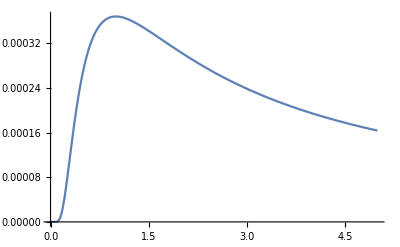

```mathematica
Plot[PDF[InverseGammaDistribution[0.001,1]][x],{x,0,5}]
```

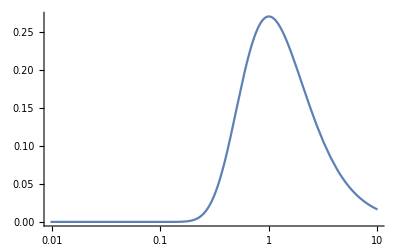

```mathematica
LogLinearPlot[PDF[InverseGammaDistribution[1,2]][x],{x,0,10}]
```